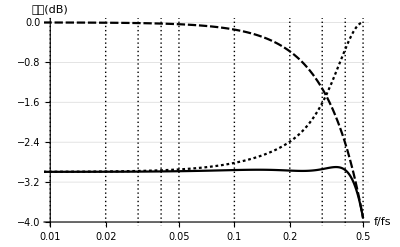

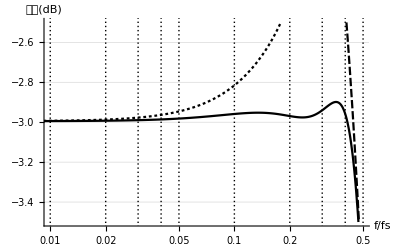

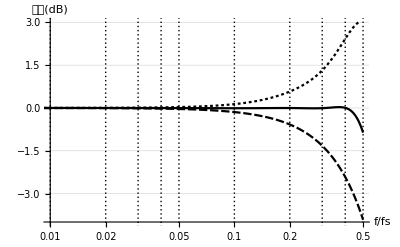

```mathematica
Gzoh[Ω_]:=Abs[Sin[Ω/2]/(Ω/2)];H1[z_]:=(-35(1+z^-6)+134(z^-1+z^-5)-562(z^-2+z^-4)+6729 z^-3)/8192;
H2[z_]:=(1(1+z^-8)-4(z^-1+z^-7)+13(z^-2+z^-6)-50(z^-3+z^-5)+592 z^-4)/512;
LogLinearPlot[{20*Log10[Abs[H1[Exp[ⅈ 2π f]]]*Gzoh[2π f]],20*Log10[Gzoh[2π f]],20*Log10[Abs[H1[Exp[ⅈ 2π f]]]]},{f,0.001,0.5},PlotTheme->"Monochrome",Ticks->{{0.01,0.02,0.05,0.1,0.2,0.5}, Automatic},PlotRange->{{0.01,0.5+0.00001},{-4,0}},GridLines->{{0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5}, Automatic},AxesLabel->{Style["f/fs",FontFamily->"Times",FontSlant->Italic,FontSize->12],Style["增益(dB)",FontFamily->"Times",FontSize->12]},AxesOrigin->{0.01,-4}]
LogLinearPlot[{20*Log10[Abs[H1[Exp[ⅈ 2π f]]]*Gzoh[2π f]],20*Log10[Gzoh[2π f]],20*Log10[Abs[H1[Exp[ⅈ 2π f]]]]},{f,0.001,0.5},PlotTheme->"Monochrome",Ticks->{{0.01,0.02,0.05,0.1,0.2,0.5}, Automatic},PlotRange->{{0.01,0.5+0.00001},{-3.5,-2.5}},GridLines->{{0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5}, Automatic},AxesLabel->{Style["f/fs",FontFamily->"Times",FontSlant->Italic,FontSize->12],Style["增益(dB)",FontFamily->"Times",FontSize->12]},AxesOrigin->{0.01,-4}]
LogLinearPlot[{20*Log10[Abs[H2[Exp[ⅈ 2π f]]]*Gzoh[2π f]],20*Log10[Gzoh[2π f]],20*Log10[Abs[H2[Exp[ⅈ 2π f]]]]},{f,0.001,0.5},PlotTheme->"Monochrome",Ticks->{{0.01,0.02,0.05,0.1,0.2,0.5}, Automatic},PlotRange->{{0.01,0.5+0.00001},{-4,3}},GridLines->{{0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5}, Automatic},AxesLabel->{Style["f/fs",FontFamily->"Times",FontSlant->Italic,FontSize->12],Style["增益(dB)",FontFamily->"Times",FontSize->12]},AxesOrigin->{0.01,-4}]
```